#### Version Notes V4 recombines LHS and RHS. “LHS_v3.2” has the fastest LHS calculations, and “RHS_calculation” is a clarified verison of Taeho’s code. This version includes further cleaned notation.

# LHS

#### Define needed operators and constants

```mathematica
snr$param = {δt-> 0.1/4, τ-> 1}; (* factor of 4 connects to Igor simulation *)
l= 0.25;
rmax = 20;
z$pauli=({{1, 0}, {0, -1}}); (*sigma z*)
ρ [θρ_]=({{(Cos[θρ/2])^2, Cos[θρ/2]*Sin[θρ/2]}, {Cos[θρ/2]*Sin[θρ/2], (Sin[θρ/2])^2}}); (*Density matrix*)
I$up=1/2(({{1, 0}, {0, 1}})+1*z$pauli); (*Pi_i=Z with eigenvalue 1*)
I$down=1/2(({{1, 0}, {0, 1}})-1*z$pauli);(*Pi_i=Z with eigenvalue -1*)
A[θa_]=({{Cos[θa], Sin[θa]}, {Sin[θa], -Cos[θa]}});
F[θf_]=({{Cos[θf], Sin[θf]}, {Sin[θf], -Cos[θf]}});
M$A$r[r_,θa_]:=√l(δt/(2π*τ))^(1/4)*MatrixExp[-δt/(4*τ) (MatrixPower[r({{1, 0}, {0, 1}})-A[θa],2])]/.snr$param;
M$A$r$dag[r_,θa_]:=√l(δt/(2π*τ))^(1/4)*MatrixExp[-δt/(4*τ) (MatrixPower[r({{1, 0}, {0, 1}})-A[θa],2])]/.snr$param;
F$up[θf_]=1/2(({{1, 0}, {0, 1}})+F[θf]); (*Pi_F with eigenvalue 1*)
F$down[θf_]=1/2(({{1, 0}, {0, 1}})-F[θf]);(*Pi_F with eigenvalue -1*)
```

Now define probabilities and entropy definitions

```mathematica
p$af$up[r_,θρ_,θa_,θf_] =Tr[F$up[θf].M$A$r[r,θa].ρ[θρ].M$A$r$dag[r,θa]];
p$af$down[r_,θρ_,θa_,θf_] = Tr[F$down[θf].M$A$r[r,θa].ρ[θρ].M$A$r$dag[r,θa]];
p$i$up[θρ_] = Tr[I$up.ρ[θρ]];
p$i$down[θρ_] = Tr[I$down.ρ[θρ]];
(*Entropies *)
H$I[θρ_]=-p$i$up[θρ] Log[2,p$i$up[θρ]] -p$i$down[θρ] Log[2,p$i$down[θρ]];
H$AF$singleR [r_,θρ_,θa_,θf_] =-p$af$up[r,θρ,θa,θf]Log[2,p$af$up[r,θρ,θa,θf]]   -p$af$down[r,θρ,θa,θf]Log[2,p$af$down[r,θρ,θa,θf]];
H$AF[θρ_,θa_,θf_] = (Sum[H$AF$singleR[r,θρ,θa,θf],
{r,-rmax+(l/2),rmax-(l/2),l}]);
LHS[θρ_,θa_,θf_]  = H$I[θρ] + H$AF[θρ,θa,θf];
```

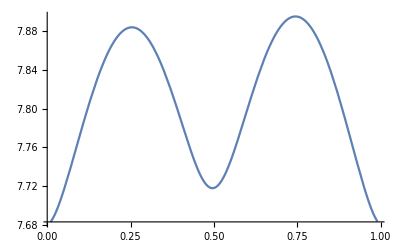
{68.2699,-Graphics-}

```mathematica
Plot[LHS[ x Pi, 0.25 Pi, 0.5 Pi], {x,0.01, 0.99}]//Timing
```

## RHS

```mathematica
params = {δt-> 0.1/4, τ-> 1,ϕf->0,ϕa->0,r0->1};
𝔽[θf_]=({{Cos[θf], Sin[θf]*Cos[ϕf]-ⅈ*Sin[θf]*Sin[ϕf]}, {Sin[θf]*Cos[ϕf]+ⅈ*Sin[θf]*Sin[ϕf], -Cos[θf]}});
ℤ=({{1, 0}, {0, -1}});
𝕏[ii_,f_,θa_,θf_]:=1/2(({{1, 0}, {0, 1}})+f*𝔽[θf])
𝕎[ii_,f_,θa_,θf_]:=1/2(({{1, 0}, {0, 1}})+ii*ℤ)
A$wkreal[ii_,f_,θa_,θf_]:=((Cos[θa] (ii+f* Cos[θf])+f* Sin[θa]* Sin[θf] )/(1+ii *f*Cos[θf]))/.params
(* We'll pre-calculate the optimal r by taking the r which minimizes RHS. See NYH Nature paper, above Eqn. D8.*)
r$opt[ii_,f_,θa_,θf_]:=A$wkreal[ii,f,θa,θf]/Log[2]/.params
P$r[rr_,ii_,f_,θa_,θf_]:=l/r0*(δt/(2π*τ))^(1/2)*Exp[-δt/(2*τ)((rr/r0)^2+1)]/.params
P$r$opt[ii_,f_,θa_,θf_] := P$r[r$opt[ii,f,θa,θf],ii,f,θa,θf]
g$r[rr_, ii_,f_,θa_,θf_]:=(rr*√l)/(r0^(3/2)*π^(1/4))(δt/(2*τ))^(5/4)*Exp[-δt/(4*τ)((rr/r0)^2+1)] /.params
g$r$opt[ii_, f_, θa_,θf_] := g$r[ r$opt[ii,f,θa,θf], ii, f, θa,θf] ;
(* Define both terms*)
RHS$T1[ii_,f_,θa_,θf_]:=-Log[2,P$r$opt[ii,f,θa,θf]*Tr[𝕏[ii,f,θa,θf].𝕎[ii,f,θa,θf]]]/.params;
RHS$T2[ii_,f_,θa_,θf_]:=-(2*Tr[𝕎[ii,f,θa,θf]])/(Log[2]*Sqrt[P$r$opt[ii,f,θa,θf]])*(g$r$opt[ii,f,θa,θf]*A$wkreal[ii,f,θa,θf])/.params; 
(*I removed a l from √Subscript[P, j] ; it should cancel with factor multiplying Subscript[g, j] as per intro doc., bottom of p.3*)
f$wk[ii_,f_,θa_,θf_]:=RHS$T1[ii,f,θa,θf] +  RHS$T2[ii,f,θa,θf]
RHS[θa_,θf_]:=Min[f$wk[1,1,θa,θf],f$wk[-1,1,θa,θf],f$wk[1,-1,θa,θf],f$wk[-1,-1,θa,θf]]
```

```mathematica
Plot3D[RHS[thetaA Pi, thetaF Pi],{thetaA,0.01,0.99}, {thetaF,0.48,0.52},AxesLabel->{"θ_A","θ_F","RHS"}]
```

-Graphics3D-

#### Find the tightest bound

```mathematica
Tightness[θρ_,θa_,θf_] = LHS[ θρ,θa,θf]-RHS[θa,θf];
```

```mathematica
tightness$tuple =Plot3D[Tightness[thetaRho Pi, thetaA Pi, thetaF Pi]/.{thetaRho-> 0.01},{thetaA,0.01,0.99}, {thetaF,0.48,0.52},AxesLabel->{"θ_A","θ_F","Tightness"}]//Timing;
Print[First@tightness$tuple]
Last@tightness$tuple
```

265.537

-Graphics3D-

```mathematica
Minimize[ LHS[(thetaRho +0.01)Pi, thetaA *Pi, thetaF *Pi]-RHS[thetaA*Pi,thetaF *Pi], {thetaRho, thetaA, thetaF}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{0.692539,{thetaRho→-1.01,thetaA→1.,thetaF→1.}}

## Misc Tests

#### Tests with 4D plots

```mathematica
Manipulate[
Show[
ContourPlot3D[x^2+x y z+z^4==c,{x,-2,2},{y,-2,2},{z,-2,2},
ContourStyle->Opacity[0.5]]],
{c,-0.25,5}]
```